```mathematica
(*This data set is representative of the relationship
 between magnetic field and angular frequency; experimental data*)

dataNMR= {{3078.32,26100*(Pi)*10^(3)},{3137.32,26600*(Pi)*10^(3)},{3173.52,26900*(Pi)*10^(3)},{3201.82,27200*(Pi)*10^(3)}}
```

{{3078.32,26100000 π},{3137.32,26600000 π},{3173.52,26900000 π},{3201.82,27200000 π}}

```mathematica
(*These are the points plotted for data set "dataNMR"; ranges are set lower that the lowest experimental value and higher than the highest experimental value*)
```

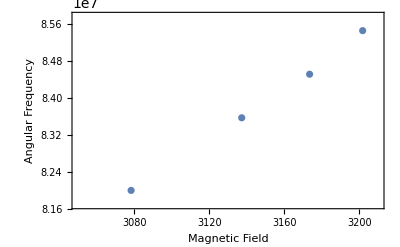

```mathematica
ListPlot[dataNMR,PlotRange->{{3050,3210},{26000*(Pi)*10^(3),27300*(Pi)*10^(3)}}, Frame->True,FrameLabel->{"Magnetic Field ","Angular Frequency"}]
```

```mathematica
(*Needs["ErrorBarPlots"] is used to bring in the error bars package*)
```

```mathematica
Needs["ErrorBarPlots`"]
```

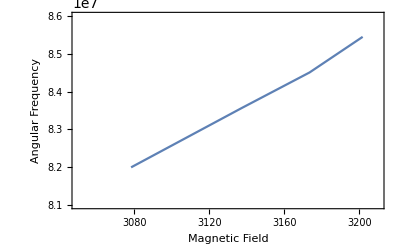

```mathematica
ErrorListPlot[{{{3078.32,26100*(Pi)*10^(3)}, ErrorBar[0.2]},{{3137.32,26600*(Pi)*10^(3)},ErrorBar[0.2]},{{3173.52,26900*(Pi)*10^(3)},ErrorBar[0.2]},{{3201.82,27200*(Pi)*10^(3)},ErrorBar[0.2]}},Frame->True,FrameLabel->{"Magnetic Field", "Angular Frequency"},PlotRange->{{3050,3210},{8.1*10^7,8.6*10^7}}, Joined -> True ]
```